```mathematica
Get["/media/storage/ciencia/investigacion/tesis/codigos-tesis/CoolTools2.m"]
Get["/media/storage/ciencia/investigacion/tesis/codigos-tesis/usefulFunctions.wl"]
<<"Quantum`"
<<"MaTeX`"
```

SetDelayed::write: Tag PermutationMatrix in PermutationMatrix[p_List] is Protected.

```mathematica
initialState = {1,0};
intialStateBV = densityMatrixToPoint[ketsToDensity[{initialState}], NQubitBasis[1]][[1]];
```

```mathematica
(*Evoluciones GUE*)
gueMatrices = RandomVariate[GaussianUnitaryMatrixDistribution[2], 30000];
```

```mathematica
evolvedStates = MatrixExp[-I 0.2 #].initialState & /@ gueMatrices;
evolvedStatesBVs = densityMatrixToPoint[ketsToDensity[evolvedStates], NQubitBasis[1]];
```

```mathematica
evolvedStatesAzimutals = #[[2]]& /@ toCylindricalCoordinates[evolvedStatesBVs, {0.,0.,1.}, {0.,0.,0.}];
```

```mathematica
(*Figuras*)
hist1 = Histogram[evolvedStatesAzimutals, Automatic, "Probability", PlotTheme->"Scientific", PlotRange->{{0, 6.1},Automatic},
				  FrameLabel->MaTeX[{"\\text{Coordenada angular}\\,(\\theta)", "\\text{Probabilidad}"}, Preamble->{"\\usepackage{newtxmath}"}]];
sphPlot1 = Show[ListPointPlot3D[evolvedStatesBVs[[1;;10000]], BoxRatios->{1, 1, 1}, PlotRange->All, PlotTheme->"Scientific",
							    AxesLabel->MaTeX[{"x", "y","z"}, Preamble->{"\\usepackage{newtxmath}"}]],
			    SphericalPlot3D[1, θ, ϕ, PlotStyle->Opacity[0.1], Mesh->None, PlotRange->All],
			    ListPointPlot3D[densityMatrixToPoint[ketsToDensity[{initialState}], NQubitBasis[1]], PlotStyle->RGBColor[0.04,0.27,0.88]]];
```

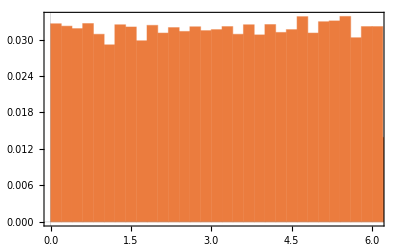
-Graphics3D- | -Graphics-

```mathematica
Grid[{{sphPlot1, hist1}}, ItemStyle->ImageSizeMultipliers->1, Spacings->{1, 1}]
```

```mathematica
SetDirectory["/media/storage/ciencia/investigacion/tesis"]
```

/media/storage/ciencia/investigacion/tesis

```mathematica
Export["figura1_apendice.pdf", %156]
```

figura1_apendice.pdf